# Example # 3 : Generic Hybrid Undulator/Wiggler

Version 0.7

## Introduction

This example creates and solves a simple multipole wiggler made with rectangular blocks. It is important to execute each section in the order of presentation. If not, errors may be reported. Any section can be edited and executed several times. To see the change in the peak field induced by the variation of the magnet size, edit the corresponding parameter in the section entitled "Create the Geometry", execute this section and re-execute the section "Solve". The section "Optimizing Parameters" provides an example of manual optimization of the pole dimensions.
To obtain acceptable precision on the magnetic field, it is essential to increase the segmentation. This is done at the expense of memory and CPU time. The segmentation in this example has been set to np={2,2,5} for the pole and nm={1,3,1} for the magnet. This corresponds to an absolute error in the peak field of the undulator/wiggler of the order of 1%. The user himself should experience consequences of   increasing np and nm and see how CPU time and memory increase, and how the value of the peak field approaches a limit which is the value looked for. To do so, edit the nm or np values in the "Create the Geometry" section, and re-execute both the "Create the Geometry" and "Solve" sections. Using segmentation which is too large segmentation may result in a memory allocation failure. To recover from such situation, the section "Load and Initialize Radia" should be re-executed. Memory allocation failure can be avoided (to some extent) by giving more memory to the Radia.exe process (Macintosh). 
It is a fact that iron pieces need much more segmentation than the magnets since the magnetization there is very sensitive to the external field.
One can also compute the Field Integral produced by such an undulator/wiggler, forces on the magnets and poles, etc. One can build a wedge pole undulator by using polyhedrons or extruded polygons instead of rectangular blocks... To learn more, read the Radia documentation, make tests and develop experience.

## Load and Initialize Radia

The following instruction loads the Radia package and returns the Radia version number. This notebook requires the Radia version 4.097 or later.

```mathematica
<<Radia`;
(* if Vector field plot is required *)
<<VectorFieldPlots`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

General::obspkg: VectorFieldPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Define Magnetic Material

The following instructions define a material by means of the Magnetization M (in Tesla) vs H (in Amp/m) dependence entered point by point. The resulting M(H) curve is plotted for verification. Note that the material is defined by calling the function "radMatSatIso" with the input parameter "ma" which contains the values of H and M both expressed in Tesla. The conversion between Amp/m and Tesla is done by multiplying H by "4*Pi*10^(-7)" when creating "ma".

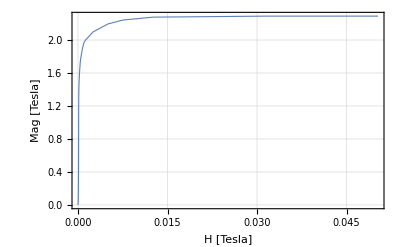

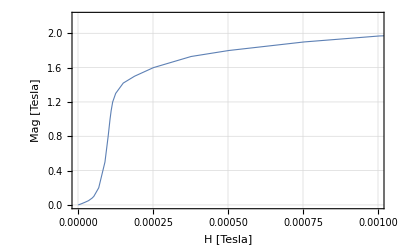

```mathematica
H = {0.8, 1.5, 2.2, 3.6, 5, 6.8, 9.8, 18, 28, 37.5, 42, 55, 71.5, 80, 85, 88, 92, 100, 120, 150, 200, 300, 400, 600, 800, 1000, 2000, 4000, 6000, 10000, 25000, 40000};

M = {0.000998995, 0.00199812, 0.00299724, 0.00499548,0.00699372, 0.00999145, 0.0149877, 0.0299774, 0.0499648, 0.0799529, 0.0999472, 0.199931, 0.49991, 0.799899, 0.999893, 1.09989, 1.19988, 1.29987, 1.41985, 1.49981, 1.59975, 1.72962, 1.7995, 1.89925, 1.96899, 1.99874,  2.09749, 2.19497, 2.24246, 2.27743, 2.28958, 2.28973};

ma =  N[Table[{H[[i]]*4*Pi*10^(-7), M[[i]]}, {i, 1, Length[H]}]];

RadPlotOptions[];
ListPlot[ma,
Joined->True,
AxesLabel->{"H [Tesla]","Mag [Tesla]"}]

ListPlot[ma,
Joined->True,
PlotRange->{{0,0.001},{0,2.2}},
AxesLabel->{"H [Tesla]","Mag [Tesla]"}]

mp=radMatSatIso[ma];
```

## Functions for odd numbers of pole (you can choose either odd or even poles)

The following function builds an array of rectangular permanent magnets with their mirror symmetric counterparts, distributes the colors, magnetic materials and sets the segmentation. The function is very generic and can be used to build almost any hybrid wiggler (without optimizing the design of terminations).

```mathematica
wig[]:=Module[{},

(* A model for odd numbers in main poles *)

(* First Principal Pole *)
y=lp[[2]]/4;
p1={{lp[[1]]/4-chp[[1]]/2,y-chp[[2]]/2,sp[[3]]},{lp[[1]]/2-chp[[1]],lp[[2]]/2-chp[[2]]}};
p2={{lp[[1]]/4,y,chp[[3]]+sp[[3]]},{lp[[1]]/2,lp[[2]]/2}};
p3={{lp[[1]]/4,y,lp[[3]]+sp[[3]]},{lp[[1]]/2,lp[[2]]/2}};
pole0=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]]/2,np[[1]]};
fullMag[pole0,npd,cp,mp];

(* First side magnet *)
If[NumPer==0,initsm={-1,0,0},initsm={1,0,0}];
s1={{(lp[[1]]-chp[[1]]+lsm[[1]]-chm[[1]])/2+sp[[1]],y-chp[[2]]/2,sp[[3]]+gapoffset},{chp[[1]]+lsm[[1]]-chm[[1]],lsm[[2]]/2-chp[[2]]}};
s2={{(lp[[1]]+lsm[[1]])/2+sp[[1]],y,chm[[3]]+sp[[3]]+gapoffset},{lsm[[1]],lsm[[2]]/2}};
s3={{(lp[[1]]+lsm[[1]])/2+sp[[1]],y,lsm[[3]]+sp[[3]]+gapoffset},{lsm[[1]],lsm[[2]]/2}};
side0=radObjMltExtRtg[{s1,s2,s3},initsm];
npd={np[[1]]/2,np[[2]]/2,np[[2]]};
nmd={nm[[1]]/2,nm[[2]]/2,nm[[2]]};
fullMag[side0,nmd,csm,mm];
y+=lp[[2]]/4;

For[i=1,i<=NumPer,i++,(
(* Periodic Magnet 1 *)
initm={0,Mod[i,2]-Mod[i+1,2],0};
y+=lm[[2]]/4+sp[[2]];
m1={{lm[[1]]/4-chm[[1]]/2,y-chm[[2]]/2,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]/2+chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
magnetP1=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP1,nmd,cm,mm];

(* Periodic Magnet 2 *)
y+=lm[[2]]/2+sp[[2]];
m1={{lm[[1]]/4-chm[[1]]/2,y+chm[[2]]/2,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]/2+chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
magnetP2=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP2,nmd,cm,mm];

(* Periodic Pole *)
y+=(lm[[2]]/2+lp[[2]])/2+sp[[2]];
p1={{lp[[1]]/4-chp[[1]]/2,y,sp[[3]]},{lp[[1]]/2-chp[[1]],lp[[2]]-2*chp[[2]]}};
p2={{lp[[1]]/4,y,chp[[3]]+sp[[3]]},{lp[[1]]/2,lp[[2]]}};
p3={{lp[[1]]/4,y,lp[[3]]+sp[[3]]},{lp[[1]]/2,lp[[2]]}};
poleP=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]],np[[1]]};
fullMag[poleP,npd,cp,mp];

(* Periodic side magnet *)
If[NumPer==0,initsm={Mod[i,2]-Mod[i+1,2],0,0},initsm={Mod[i+1,2]-Mod[i,2],0,0}];
s1={{(lp[[1]]-chp[[1]]+lsm[[1]]-chm[[1]])/2+sp[[1]],y,sp[[3]]+gapoffset},{chp[[1]]+lsm[[1]]-chm[[1]],lsm[[2]]-2*chp[[2]]}};
s2={{(lp[[1]]+lsm[[1]])/2+sp[[1]],y,chm[[3]]+sp[[3]]+gapoffset},{lsm[[1]],lsm[[2]]}};
s3={{(lp[[1]]+lsm[[1]])/2+sp[[1]],y,lsm[[3]]+sp[[3]]+gapoffset},{lsm[[1]],lsm[[2]]}};
sideP=radObjMltExtRtg[{s1,s2,s3},initsm];
npd={np[[1]]/2,np[[2]],np[[2]]};
nmd={nm[[1]]/2,nm[[2]],nm[[2]]};
fullMag[sideP,nmd,csm,mm];
y+=lp[[2]]/2;

If[i==1,magnet1=radObjCnt[{magnetP1,magnetP2}],radObjAddToCnt[magnet1,{magnetP1,magnetP2}]];
If[i==1,pole1=radObjCnt[{poleP}],radObjAddToCnt[pole1,{poleP}]];
If[i==1,side1=radObjCnt[{sideP}],radObjAddToCnt[side1,{sideP}]];
(*radObjAddToCnt[und,{poleP,mangetP1,magnetP2,sideP}];*)
)];

(* Magnet before End pole *)
initm={0,Mod[NumPer+1,2]-Mod[NumPer,2],0};
y+=lm[[2]]/2+sp[[2]];
m1={{lm[[1]]/4-chm[[1]]/2,y,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]+2*chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]}};
magnet2=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]]*2,nm[[2]]};
fullMag[magnet2,nmd,cm,mm];

(* End pole *)
y+=(lm[[2]]+lep[[2]])/2+sp[[2]]+dpm[[1]];
p1={{lep[[1]]/4-chp[[1]]/2,y,sp[[3]]},{lep[[1]]/2-chp[[1]],lep[[2]]-2*chp[[2]]}};
p2={{lep[[1]]/4,y,chp[[3]]+sp[[3]]},{lep[[1]]/2,lep[[2]]}};
p3={{lep[[1]]/4,y,lep[[3]]+sp[[3]]},{lep[[1]]/2,lep[[2]]}};
pole2=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]]/2,np[[1]]};
fullMag[pole2,npd,cp,mp];

(* End side magnet *)
initsm={Mod[NumPer,2]-Mod[NumPer+1,2],0,0};
s1={{(lep[[1]]-chp[[1]]+les[[1]]-chm[[1]])/2+sp[[1]],y,sp[[3]]+gapoffset},{chp[[1]]+les[[1]]-chm[[1]],les[[2]]-2*chp[[2]]}};
s2={{(lep[[1]]+les[[1]])/2+sp[[1]],y,chm[[3]]+sp[[3]]+gapoffset},{les[[1]],les[[2]]}};
s3={{(lep[[1]]+les[[1]])/2+sp[[1]],y,les[[3]]+sp[[3]]+gapoffset},{les[[1]],les[[2]]}};
side2=radObjMltExtRtg[{s1,s2,s3},initsm];
npd={np[[1]]/2,np[[2]]/2,np[[2]]};
nmd={nm[[1]]/2,nm[[2]]/2,nm[[2]]};
fullMag[side2,nmd,csm,mm];

(* End magnet for half size and unit model *)
initm={0,Mod[NumPer,2]-Mod[NumPer+1,2],0};
If[(NumPer==0)||(ending==0),y+=lm[[2]]/4+lep[[2]]/2-lm[[2]]-lep[[2]]-sp[[2]]-dpm[[1]],y+=lm[[2]]/4+lep[[2]]/2+sp[[2]]+dpm[[2]]];
m1={{lm[[1]]/4-chm[[1]]/2,y-chm[[2]]/2,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]/2+chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
magEnd=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magEnd,nmd,cm,mm];

If[NumPer==0,magnet=radObjCnt[{magEnd}],magnet=radObjCnt[{magnet1,magnet2,magEnd}]];
If[NumPer==0,pole=radObjCnt[{pole0}],pole=radObjCnt[{pole0,pole1,pole2}]];
If[NumPer==0,side=radObjCnt[{side0}],side=radObjCnt[{side0,side1,side2}]];
If[NumPer==0,und=radObjCnt[{pole0,side0}],und=radObjCnt[{pole0,pole1,side0,side1,magnet1}]];
If[(NumPer==0)||(ending==0),radObjAddToCnt[und,{magEnd}],radObjAddToCnt[und,{magnet2,pole2,side2,magEnd}]];

tr=radTrfTrsl[{0,0,gap/2}];
radTrfOrnt[magnet,tr];
radTrfOrnt[pole,tr];
radTrfOrnt[side,tr];
radTrfOrnt[und,tr];

(* Mirrors *)
RadTrfZerPerp[und,{0,0,0},{1,0,0}];
If[(NumPer==0)&&(ending==0),"",RadTrfZerPara[und,{0,0,0},{0,0,1}]];
RadTrfZerPerp[und,{0,0,0},{0,1,0}];

RadTrfZerPerp[magnet,{0,0,0},{1,0,0}];
(*If[(NumPer==0),"",RadTrfZerPara[magnet,{0,0,0},{0,0,1}]];*)
RadTrfZerPerp[magnet,{0,0,0},{0,1,0}];

RadTrfZerPerp[pole,{0,0,0},{1,0,0}];
(*If[(NumPer==0),"",RadTrfZerPara[pole,{0,0,0},{0,0,1}]];*)
RadTrfZerPerp[pole,{0,0,0},{0,1,0}];
poleF=radObjCnt[{pole}];
RadTrfZerPara[poleF,{0,0,0},{0,0,1}];

RadTrfZerPerp[side,{0,0,0},{1,0,0}];
(*If[(NumPer==0),"",RadTrfZerPara[side,{0,0,0},{0,0,1}]];*)
RadTrfZerPerp[side,{0,0,0},{0,1,0}];

undfrc=radObjCnt[{side,pole,magnet}];

(*undc=radObjCutMag[und,{0,0,40},{0,0,1},Frame->Lab][[1]];*)
(*Print["Total length (",NumPer*2+1," poles):    ",N[(y+lm[[2]]/4)*2,5],"  mm"];*)
totallength=N[(y+lm[[2]]/4)*2,5];
numpoles=NumPer*2+1;
und
]
```

## Functions for even numbers of pole (you can choose either odd or even poles)

The following function builds an array of rectangular permanent magnets with their mirror symmetric counterparts, distributes the colors, magnetic materials and sets the segmentation. The function is very generic and can be used to build almost any hybrid wiggler (without optimizing the design of terminations).

```mathematica
wig[]:=Module[{},

(* A model for even numbers in main poles *)
y=0;
For[i=1,i<=NumPer,i++,(
(* Periodic Magnet 1 *)
initm={0,Mod[i,2]-Mod[i+1,2],0};
If[i==1,y+=lm[[2]]/4+sp[[2]]/2,y+=lm[[2]]/4+sp[[2]]];
m1={{lm[[1]]/4-chm[[1]]/2,y+chm[[2]]/2,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]/2+chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
magnetP1=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP1,nmd,cm,mm];

(* Periodic Pole *)
y+=(lm[[2]]/2+lp[[2]])/2+sp[[2]];
p1={{lp[[1]]/4-chp[[1]]/2,y,sp[[3]]+gapoffset},{lp[[1]]/2-chp[[1]],lp[[2]]-2*chp[[2]]}};
p2={{lp[[1]]/4,y,chp[[3]]+sp[[3]]+gapoffset},{lp[[1]]/2,lp[[2]]}};
p3={{lp[[1]]/4,y,lp[[3]]+sp[[3]]+gapoffset},{lp[[1]]/2,lp[[2]]}};
poleP=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]],np[[1]]};
fullMag[poleP,npd,cp,mp];

(* Periodic side magnet *)
If[NumPer==0,initsm={Mod[i,2]-Mod[i+1,2],0,0},initsm={Mod[i+1,2]-Mod[i,2],0,0}];
s1={{(lp[[1]]-chp[[1]]+lsm[[1]]-chm[[1]])/2+sp[[1]],y,sp[[3]]+gapoffset},{chp[[1]]+lsm[[1]]-chm[[1]],lsm[[2]]-2*chp[[2]]}};
s2={{(lp[[1]]+lsm[[1]])/2+sp[[1]],y,chm[[3]]+sp[[3]]+gapoffset},{lsm[[1]],lsm[[2]]}};
s3={{(lp[[1]]+lsm[[1]])/2+sp[[1]],y,lsm[[3]]+sp[[3]]+gapoffset},{lsm[[1]],lsm[[2]]}};
sideP=radObjMltExtRtg[{s1,s2,s3},initsm];
npd={np[[1]]/2,np[[2]],np[[2]]};
nmd={nm[[1]]/2,nm[[2]],nm[[2]]};
fullMag[sideP,nmd,csm,mm];

(* Periodic Magnet 2 *)
initm={0,Mod[i+1,2]-Mod[i,2],0};
y+=(lm[[2]]/2+lp[[2]])/2+sp[[2]];
m1={{lm[[1]]/4-chm[[1]]/2,y-chm[[2]]/2,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]/2+chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
magnetP2=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP2,nmd,cm,mm];

y+=lm[[2]]/4;

If[i==1,magnet1=radObjCnt[{magnetP1,magnetP2}],radObjAddToCnt[magnet1,{magnetP1,magnetP2}]];
If[i==1,pole1=radObjCnt[{poleP}],radObjAddToCnt[pole1,{poleP}]];
If[i==1,side1=radObjCnt[{sideP}],radObjAddToCnt[side1,{sideP}]];
(*radObjAddToCnt[und,{poleP,mangetP1,magnetP2,sideP}];*)
)];

(* Magnet before End pole *)
initm={0,Mod[NumPer+1,2]-Mod[NumPer,2],0};
y+=lm[[2]]/4+sp[[2]];
m1={{lm[[1]]/4-chm[[1]]/2,y+chm[[2]]/2,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]/2+chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
magnet2=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnet2,nmd,cm,mm];

(* End pole *)
y+=(lm[[2]]/2+lep[[2]])/2+sp[[2]]+dpm[[1]];
p1={{lep[[1]]/4-chp[[1]]/2,y,sp[[3]]},{lep[[1]]/2-chp[[1]],lep[[2]]-2*chp[[2]]}};
p2={{lep[[1]]/4,y,chp[[3]]+sp[[3]]},{lep[[1]]/2,lep[[2]]}};
p3={{lep[[1]]/4,y,lep[[3]]+sp[[3]]},{lep[[1]]/2,lep[[2]]}};
pole2=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]]/2,np[[1]]};
fullMag[pole2,npd,cp,mp];

(* End side magnet *)
initsm={Mod[NumPer,2]-Mod[NumPer+1,2],0,0};
s1={{(lep[[1]]-chp[[1]]+les[[1]]-chm[[1]])/2+sp[[1]],y,sp[[3]]+gapoffset},{chp[[1]]+les[[1]]-chm[[1]],les[[2]]-2*chp[[2]]}};
s2={{(lep[[1]]+les[[1]])/2+sp[[1]],y,chm[[3]]+sp[[3]]+gapoffset},{les[[1]],les[[2]]}};
s3={{(lep[[1]]+les[[1]])/2+sp[[1]],y,les[[3]]+sp[[3]]+gapoffset},{les[[1]],les[[2]]}};
side2=radObjMltExtRtg[{s1,s2,s3},initsm];
npd={np[[1]]/2,np[[2]]/2,np[[2]]};
nmd={nm[[1]]/2,nm[[2]]/2,nm[[2]]};
fullMag[side2,nmd,csm,mm];

(* End magnet for half size and unit model *)
initm={0,Mod[NumPer,2]-Mod[NumPer+1,2],0};
y+=lm[[2]]/4+lep[[2]]/2+sp[[2]]+dpm[[2]];
m1={{lm[[1]]/4-chm[[1]]/2,y-chm[[2]]/2,sp[[3]]+gapoffset},{lm[[1]]/2-chm[[1]],lm[[2]]/2+chm[[2]]}};
m2={{lm[[1]]/4,y,chm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
m3={{lm[[1]]/4,y,lm[[3]]+sp[[3]]+gapoffset},{lm[[1]]/2,lm[[2]]/2}};
magEnd=radObjMltExtRtg[{m1,m2,m3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magEnd,nmd,cm,mm];

If[NumPer==0,magnet=radObjCnt[{magnet2,magEnd}],magnet=radObjCnt[{magnet1,magnet2,magEnd}]];
If[NumPer==0,pole=radObjCnt[{pole2}],pole=radObjCnt[{pole1,pole2}]];
If[NumPer==0,side=radObjCnt[{side2}],side=radObjCnt[{side1,side2}]];
If[NumPer==0,und=radObjCnt[{pole2,side2,magnet2,magEnd}],und=radObjCnt[{pole1,side1,magnet1}]];
If[(NumPer>0) && (ending==0),"",radObjAddToCnt[und,{magnet2,pole2,side2,magEnd}]];

tr=radTrfTrsl[{0,0,gap/2}];
radTrfOrnt[magnet,tr];
radTrfOrnt[pole,tr];
radTrfOrnt[side,tr];
radTrfOrnt[und,tr];

(* Mirrors *)
RadTrfZerPerp[und,{0,0,0},{1,0,0}];
If[(NumPer==0)&&(ending==0),"",RadTrfZerPara[und,{0,0,0},{0,0,1}]];
RadTrfZerPara[und,{0,0,0},{0,1,0}];

RadTrfZerPerp[magnet,{0,0,0},{1,0,0}];
(*If[(NumPer==0),"",RadTrfZerPara[magnet,{0,0,0},{0,0,1}]];*)
RadTrfZerPara[magnet,{0,0,0},{0,1,0}];

RadTrfZerPerp[pole,{0,0,0},{1,0,0}];
(*If[(NumPer==0),"",RadTrfZerPara[pole,{0,0,0},{0,0,1}]];*)
RadTrfZerPara[pole,{0,0,0},{0,1,0}];

RadTrfZerPerp[side,{0,0,0},{1,0,0}];
(*If[(NumPer==0),"",RadTrfZerPara[side,{0,0,0},{0,0,1}]];*)
RadTrfZerPara[side,{0,0,0},{0,1,0}];

undfrc=radObjCnt[{side,pole,magnet}];

(*undc=radObjCutMag[und,{0,0,40},{0,0,1},Frame->Lab][[1]];*)
(*Print["Total length (",NumPer*2," poles):    ",N[(y+lm[[2]]/4)*2,5],"  mm"];*)
totallength=N[(y+lm[[2]]/4)*2,5];
numpoles=NumPer*2;
und
]
```

## Create Geometry

The following instructions build an undulator with NdFeB magnets and poles  made with the material previously defined. One could also use a Radia predefined steel by replacing "mp=radMatSatIso[ma]" with "mp=RadMatAFK502[]" or "m=RadMatXc06[]" or "m=RadMatSteel42[]". See the section "How to get Help" later on to obtain the full specification of any of the material predefined in Radia .

```mathematica
radUtiDelAll[];

(* General Parameters: gap, # of periods, unit length, offset (not used), and ending suppresion on:0/off:1 *)
gap=20;NumPer=2;per=220;gapoffset=0;ending=1;zer={0,0,0};

(* Spacing Parameters for exploded view *)
sp={0,0,0};

(* Pole Parameters, lengths in x,y,z, # of subdivision, color, and chamfer *)
lp={70,35,90};np={2,2};cp={1,0,1};chp={9,0,10};

(* Magnet Parameters, chamber: x(outer), y(inner), z(depth) *)
lm={120,per/2-lp[[2]],130};nm={2,2};cm={0,1,1};chm={10,0,10};

(* Side Magnet Parameters *)
lsm={(lm[[1]]-lp[[1]])/2,lp[[2]],110};csm={0,0.5,1};

(* End Pole Parameters *)
lep={lp[[1]],20,lp[[3]]};

(* End Side Magnet Parameters *)
(*les={lsm[[1]],lep[[2]],80};*)
les={lsm[[1]],lep[[2]],34.0};

(* Ending gaps: gap to end pole, gap to end mag *)
dpm={0,0};

(* Define Pole Material *)
mp=RadMatAFK502[];
(*mp=radMatSatIso[ma];*)

(* Define NdFeB with 1.2 Tesla Remanent Magnetization *)
mm=RadMatNdFeB[1.2];

(* Define function to assign segmentation, color, material *)
fullMag[u_,x_,y_,z_]:=(radObjDivMag[u,x];radObjDrwAtr[u,y];radMatApl[u,z]);

(* Build the Structure *)
und=wig[];

Print["Total length (",numpoles," poles): ",totallength," mm"];
```

Total length (1 poles): 110. mm

## Plot Geometry

The following instructions create a set of 3D graphical primitives representing the structure in space, and plot it.

```mathematica
draw=radObjDrw[und];

RadPlot3DOptions[];
Show[Graphics3D[draw]
,ViewPoint->{5,-1.5,2}
,PlotRange->All]
```

## Solve

The following instructions Solve for the magnetization of each sub-block which constitutes the wiggler.

```mathematica
t0=AbsoluteTime[];
re=RadSolve[und,0.0003,1000];
t1=AbsoluteTime[];

Print["Solved in : ",Round[t1-t0]," seconds"];
Print["Number of Iterations : ",re[[4]]];
Print["Average Stability of Magnetization at the last iteration : ",N[re[[1]],2]," T"];
Print["Maximum Absolute Magnetization at the last iteration : ",N[re[[2]],4]," T"];
Print["Maximum H vector at the last iteration : ",N[re[[3]],4]," T"];
Print[""];
Print["Central (odd) Field Bz(0,0,0) : ",N[radFld[und,"Bz",zer],4]," T"];
Print["Even-pole Field Bz(0,",-per/4,",0) : ",N[radFld[und,"Bz",{0,-per/4,0}],4]," T"];
```

## Plot the Magnetic Field

```mathematica
RadPlotOptions[];
Plot[radFld[und,"Bz",{0,y,0}],{y,-(NumPer+1)/1*per,(NumPer+1)/1*per}
,AxesOrigin->{0,0}
,RotateLabel->True
,FrameLabel->{"Y [mm]","Bz [T]","X = Z =  0",""}]
t=Table[{y, radFld[und,"Bz",{0,y,0}]},{y,-(NumPer+1)/1*per,(NumPer+1)/1*per}];
Export[FileNameJoin[{NotebookDirectory[],"Field_y.dat"}],t]
```

```mathematica
RadPlotOptions[];
Plot[radFld[und,"Bz",{x,0,0}],{x,-100,100}
,AxesOrigin->{0,0}
,RotateLabel->True
,FrameLabel->{"X [mm]","Bz [T]","Y = Z =  0",""}]
t=Table[{x, radFld[und,"Bz",{x,0,0}]},{x,-100,100}];
Export[FileNameJoin[{NotebookDirectory[],"Field_x.dat"}],t]
```

## Checking the Magnetic Material

This cell presents a plot of the Magnetization vs Field Strength for the materials in use. Note that the NdFeB is anisotropic.

```mathematica
RadPlotOptions[];
Plot[radMatMvsH[pole, "mz", {0,0,hz}],{hz,-0.01,0.01}
,FrameLabel->"Pole Material "
,AxesLabel->{"H","M"}
]

Plot[
{radMatMvsH[magnet, "mz", {0,0,h}]
,radMatMvsH[magnet, "my", {0,h,0}]}
,{h,-1,1}
,FrameLabel->"NdFeB"
,AxesLabel->{"H","M"}
]
```

Radia::Error025: Incorrect input: Element with that key is neither Material nor 3D object with Material applied.

General::stop: Further output of Radia::Error025 will be suppressed during this calculation.

-Graphics-

Radia::Error025: Incorrect input: Element with that key is neither Material nor 3D object with Material applied.

General::stop: Further output of Radia::Error025 will be suppressed during this calculation.

-Graphics-

## Plot the Beam Trajectory

```mathematica
trj=radFldPtcTrj[und,1.2,{0,0,0,0},{-2000,2000},1001];
(*trjy=Table[x, {x, -2000, 2000, 4}];*)
trjy=trj[[All,1]];
trjx=trj[[All,2]];
t2=Table[{trjy[[z]], trjx[[z]]}, {z, 1, 1001}];
Export[FileNameJoin[{NotebookDirectory[],"Trajectory_x0.dat"}],t2]
ListLinePlot[t2,PlotRange->{{-(NumPer+2)*(per*2/3),(NumPer+2)*(per*2/3)}, {-0.5,1.2}}
,Frame->True,FrameLabel->{"Y [mm]","Trajectory [mm]"," Z = 0 ",""}
,RotateLabel->True,GridLines->Automatic, PlotStyle->{Thickness[0.002]}]

trja=1000*trj[[All,3]];
t3=Table[{trjy[[z]], trja[[z]]}, {z, 1, 1001}];
Export[FileNameJoin[{NotebookDirectory[],"Trajectory_x1.dat"}],t3]
ListLinePlot[t3,PlotRange->{{-(NumPer+2)*(per*2/3),(NumPer+2)*(per*2/3)},{-20, 20}}
,Frame->True,FrameLabel->{"Y [mm]","Angle [mrad]"," Z = 0 ",""}
,RotateLabel->True,GridLines->Automatic, PlotStyle->{Thickness[0.002]}]
```

## Plot the Field Integrals

```mathematica
int=Plot[radFldInt[und,"inf","ibz",{x,-1500,0},{x,1500,0}],{x,-300,300},
FrameLabel->{"X [mm]","IBz [T mm]","Z = 0",""},
RotateLabel->True]
(* which means the integral between y = -1500 to 1500 for each x ranging from -300 to 300 *)
(*Print[int[[1,1,1,3,1,2,1]]];*)
inty=int[[1,1,1,3,1,2,1]];
t=Table[inty];
Export[FileNameJoin[{NotebookDirectory[],"Fieldint_x.dat"}],t]
```

## Magnetization field vector

Plot the magnetization in the center of each subdivided element of the magnet.

```mathematica
RadPlot3DOptions[];
fldvec=ListVectorFieldPlot3D[radObjM[und]
,VectorHeads->True
,ColorFunction-> Hue
,PlotLabel->"Magnetization in Element # "
,ViewPoint->{3,2, 0}
,PlotRange->{All,All,All} 
,ScaleFactor->15]
(*Print[fldvec[[1,2;; ;; 5,1,1]]]*)
(*Print[fldvec[[1,1;; ;;5]]]*)
t0=Table[fldvec[[1  ,2 ;; ;; 5,1, 1]]];
Export[FileNameJoin[{NotebookDirectory[],"Mag_pos.dat"}],t0]
t1=Table[fldvec[[1  ,2 ;; ;; 5, 1,2]]];
Export[FileNameJoin[{NotebookDirectory[],"Mag_vec.dat"}],t1]
```

## Magnetic Force

One computes the force over the element pole induced by the whole structure. One should be cautious that the cpu time to compute the force can be very long and one must set the segmentation parameter k to the lowest values consistent with sufficient precision. Taking into account the symmetry with respect to the x axis {1,0,0} would remove the Fx component and double the Fy and Fz components.

```mathematica
k={1,1,4};
t1=AbsoluteTime[];
fr=radFldEnrFrc[pole,und,"",k];
t2=AbsoluteTime[];
Print["{Fx, Fy, Fz} = ",N[fr,3]," Newton"];
Print ["cpu time : ",N[t2-t1,3]," seconds"];
```

## Optimizing Parameters in pole and PM dimensions

In this section, some iterations are made on solving and computing the peak field of the wiggler as a function of the horizontal width of the pole. The segmentation in the pole and magnet has been set to {1,1,1} resulting in a quick but inaccurate computation.

```mathematica
gap=20;NumPer=2;per=220;gapoffset=0;ending=1;zer={0,0,0};sp={0,0,0};
(*lsm={(lm[[1]]-lp[[1]])/2,lp[[2]],110};csm={0,0.5,1};
lep={lp[[1]],20,lp[[3]]};
les={lsm[[1]],lep[[2]],80};
dpm={0,dpm[[1]]};*)

lp={70,35,90};np={2,np[[1]]};cp={1,0,1};chp={9,chp[[1]],10};
lm={180,per/2-lp[[2]],130};nm={2,nm[[1]]};cm={0,1,1};chm={10,chp[[1]],10};

(*lp={70,per/2-lm[[2]],90};np={2,2};cp={1,0,1};
lm={120,75,130};nm={2,2};cm={0,1,1};*)

(*lp={70,(per*35/2)/110,90};np={2,2};cp={1,0,1};
lm={120,per/2-lp[[2]],130};nm={2,2};cm={0,1,1};*)

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.2];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFld[und,"Bz",{0,0,0}],4]
]

t=Table[{y,(lp[[1]]=y;F[])},{y,10,120,5}];
(*t=Table[{y,(lm[[3]]=y;F[])},{y,50,200,5}];*)
(*t=Table[{y,(per=y;F[])},{y,100,300,20}];*)
(*t=Table[{y,(NumPer=y;F[])},{y,1,5,1}];*)
(*t=Table[{y,(np[[1]]=y;F[])},{y,1,5,1}];*)
(*t=Table[{y,(nm[[1]]=y;F[])},{y,1,5,1}];*)
(*t=Table[{y,(nm[[1]]=y;F[])},{y,1,5,1}];*)
(*t=Table[{y,(chp[[1]]=y;F[])},{y,1,15,1}];*)
Export[FileNameJoin[{NotebookDirectory[],"maxField_lpx_gap20_lmx180.dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"NumPer","Peak Field"}]
```

## Field integral upon gap, distance to ending units or end side magnet height

In this section, some iterations are made on solving and computing the peak field of the wiggler as a function of the horizontal width of the pole. The segmentation in the pole and magnet has been set to {1,1,1} resulting in a quick but inaccurate computation.

```mathematica
gap=15;NumPer=2;per=220;gapoffset=0;ending=1;zer={0,0,0};sp={0,0,0};
les={lsm[[1]],lep[[2]],80};
dpm={0,dpm[[1]]};

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.29];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFldInt[und,"inf","ibz",{0,-2000,0},{0,2000,0}],3]
]

t=Table[{y,(gap=y;F[])},{y,5,100,5}];
(*t=Table[{y,(dpm[[1]]=y;F[])},{y,0,20,1}];*)
(*t=Table[{y,(les[[3]]=y;F[])},{y,60,90,1}];*)
Export[FileNameJoin[{NotebookDirectory[],"fldint_gap.dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"lesz","fldint"}]
```

```mathematica
(* Plot field integral in x axis upon gap, lpx, lesz *)
gap=15;NumPer=2;per=220;gapoffset=0;ending=1;zer={0,0,0};sp={0,0,0};
lp={70,35,90};np={2,2};cp={1,0,1};
lm={120,per/2-lp[[2]],130};nm={2,2};cm={0,1,1};
les={lsm[[1]],lep[[2]],80};
dpm={0,dpm[[1]]};

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.29];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFldInt[und,"inf","ibz",{x,-2000,0},{x,2000,0}],3]
]

t=Table[{y,(x=y;F[])},{y,-20,20,2}];
Export[FileNameJoin[{NotebookDirectory[],"fldint_x_lesz80_gap15.dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"lesz","fldint"}]
```

## Magnetic force upon gap

In this section, some iterations are made on solving and computing the peak field of the wiggler as a function of the horizontal width of the pole. The segmentation in the pole and magnet has been set to {1,1,1} resulting in a quick but inaccurate computation.

```mathematica
gap=20;NumPer=2;per=220;gapoffset=0;
lp={70,35,90};np={2,2};cp={1,0,1};
lm={120,per/2-lp[[2]],130};nm={2,2};cm={0,1,1};

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.29];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFldEnrFrc[pole,und,"",{1,1,4}][[3]],3]
]

t=Table[{y,(gap=y;F[])},{y,5,200,5}];
Export[FileNameJoin[{NotebookDirectory[],"force_gap.dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"Gap","Force"}]

(*t=Table[{y,(NumPer=y;F[])},{y,1,5,1}];
Export[FileNameJoin[{NotebookDirectory[],"force_pole_odd.dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"Pole","Force"}]*)
```

## How to Get Help

The following command lists all the functions defined in the Radia.exe  file.

```mathematica
?rad*
```

The following command gives the template and the description of the function  "radObjArcCur".

```mathematica
?RadPlot3DOptions
```

The following command lists all the functions defined in the Init.m file. These functions are fully written in Mathematica code

```mathematica
?Rad*
```

The following command gives the full mathematica definition of the function "RadMatAFK502" as defined in Mathematica.

```mathematica
??RadMatXc06
```

Information[RadMatXc06,LongForm→True]